```mathematica
ClearAll["Global`*"];
U1=420.+69ⅉ;
U2=42.-42ⅉ;
A=Abs[U2/U1]
AmpU1=Abs[U1]
AmpU2=Abs[U2]
φ1=Arg[U1]
φ2=Arg[U2]
φ2-φ1
Arg[U2/U1]
```

0.139551

425.63

59.397

0.162831

-0.785398

-0.948229

-0.948229

1/(1/10000+(ⅈ ω)/100000000)

10000+(ⅈ ω)/100

10000+1/(1/10000+(ⅈ ω)/100000000)+(ⅈ ω)/100

(10000+(ⅈ ω)/100)/(10000+1/(1/10000+(ⅈ ω)/100000000)+(ⅈ ω)/100)

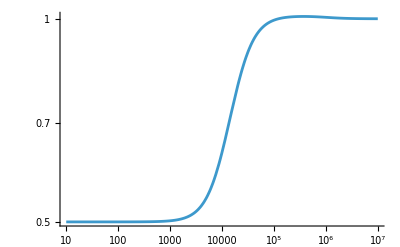

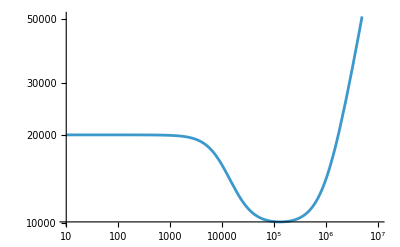

```mathematica
ClearAll["Global`*"];
u=4.2+3.1ⅉ;
r1=10*10^3;
r2=10*10^3;
c=10*10^-9;
l=10*10^-3;

zr1=r1;
zr2=r2;
zc=1/(ⅉ*ω*c);
zl=ⅉ*ω*l;

z1=1/(1/zr1+1/zc)
z2=zr2+zl

zin=z2+z1

a=z2/zin

LogLogPlot[Abs[a],{ω,10,10^7}]
LogLogPlot[Abs[zin],{ω,10,10^7}]
```

```mathematica
ClearAll["Global`*"];
k1=10;k2=8;

adb=k1+k2 

Solve[-adb==20.*Log10[Abs[A]],A]
```

18

{{A→0.125893}}

```mathematica
ClearAll["Global`*"];
u1=10;u2=5;
k1=-5; k2=-3;
(*zisk1=-k1;zisk2=-k2;*)

res1=Solve[k1==20.*Log10[Abs[uA/u1]],uA]
res2=Solve[k2==20.*Log10[Abs[u2/uB]],uB]

a3=uB/uA/.res1/.res2
20.*Log10[Abs[a3]]
```

{{uA→5.62341}}

{{uB→7.06269}}

{{1.25594}}

{{1.9794}}

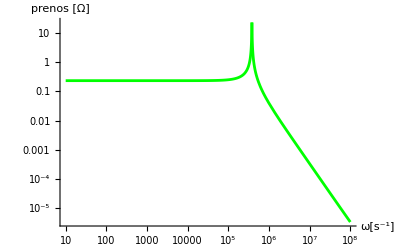

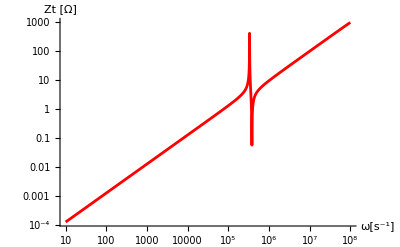

```mathematica
ClearAll["Global`*"];
ClearAll["Global`*"];
t=(2*π)/ω;
u1=10*Sin[100*t+1.5];
u1f=10+ⅇ^(ⅉ*1.5);
r1=5*10^3;
r2=100*10^3;
c=3*10^-6;
l1=10*10^-6;
l2=3*10^-6;

zr1=r1;
zr2=r2;
zc=1/(ⅉ*ω*c);
zl1=ⅉ*ω*l1;
zl2=ⅉ*ω*l2;

z1=1/(1/zr1+1/zl1);

z2=1/(1/zr2+1/zl2+1/zc);

zin=z2+z1;

a=z2/zin;




LogLogPlot[Abs[a],{ω,10,10^8},AxesLabel->{"ω[s^-1]","prenos [Ω]"},PlotStyle->Green]
LogLogPlot[Abs[zin],{ω,10,10^8},AxesLabel->{"ω[s^-1]","Zt [Ω]"},PlotStyle->Red]
```